```mathematica
τ=10.^-2;

explicitCoeffs={
{1.,0,0,0,0},
{3./2,-1./2,0,0,0},
{23./12,-16./12,5./12,0,0},
{55./24,-59./24,37./24,-9./24,0},
{1901./720,-2774./720,2616./720,-1274./720,251./720}
};
explicitVars[func_,f_,x_]:={func[x-τ,f[Round[x-τ,τ]]],func[x-2τ,f[Round[x-2τ,τ]]],func[x-3τ,f[Round[x-3τ,τ]]],func[x-4τ,f[Round[x-4τ,τ]]],func[x-5τ,f[Round[x-5τ,τ]]]};

implicitCoeffs={
{1./2,1./2,0,0,0},
{5./12,8./12,-1./12,0,0},
{9./24,19./24,-5./24,1./24,0},
{251./720,646./720,-264./720,106./720,-19./720}
};
implicitVars[func_,f_,x_]:={func[x,f[Round[x,τ]]],func[x-τ,f[Round[x-τ,τ]]],func[x-2τ,f[Round[x-2τ,τ]]],func[x-3τ,f[Round[x-3τ,τ]]],func[x-4τ,f[Round[x-4τ,τ]]]};

difference[type_,func_,f_,x_,m_]:=Module[{coeffs, vars},
If[type=="Implicit",
coeffs=implicitCoeffs;vars:=implicitVars,
coeffs=explicitCoeffs;vars:=explicitVars];

Return[τ coeffs[[m]].vars[func,f,x]];
];
```

```mathematica
AdamsMethod[type_,func_,m_,startX_,endX_,startY_]:=Module[{f},
f[Round[startX,τ]]=startY;
Do[
f[Round[startX+i τ,τ]]=First[
Flatten[NSolveValues[f[Round[startX+i τ,τ]]==f[Round[startX+(i -1)τ,τ]]+difference["Explicit",func,f,Round[startX+i τ,τ],i],{f[Round[startX+i τ,τ]]}]]];
Print[f[Round[startX+i τ,τ]]];
,{i,1,m-1}];
Do[
f[Round[startX+i τ,τ]]=f[Round[startX+i τ,τ]]/.Flatten[
FindRoot[
f[Round[startX+i τ,τ]]==f[Round[startX+(i -1)τ,τ]]+difference[type,func,f,Round[startX+i τ,τ],m],{f[Round[startX+i τ,τ]],f[Round[startX+(i-1) τ,τ]]}
]
];
,{i,m,(endX-startX)/τ}
];
Return[f];
];
```

```mathematica
func[x_,y_]:=(2x y)/(3 x^2-y^2);
fres=AdamsMethod["Implicit",func,4,1.,10.,1.];
```

1.01

1.02

1.03

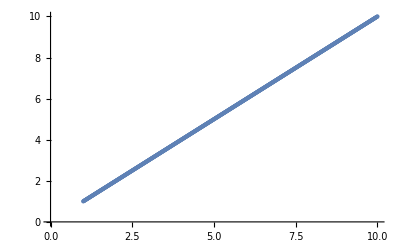

```mathematica
p={};
For[i=1.,i<=10,i+=τ,AppendTo[p,{i,fres[Round[i,τ]]}]];
ListPlot[p]
```

InterpolatingFunction[…][x]

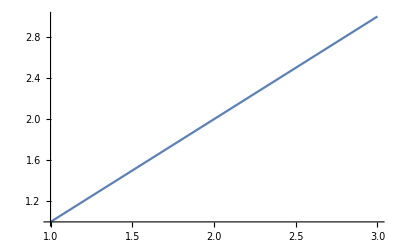

```mathematica
eqs={
y'[x]==(2x y[x])/(3 x^2-y[x]^2),
y[1]==1
};
U=NDSolveValue[eqs,y[x],{x,1,3}]
Plot[U,{x,1,3},PlotRange->All]
```

```mathematica
β=0.77;
μ=0.1;
k=0.97;
γ=0.037;
d=0;
τ1=1;

tmax=10;

Clear[r,e,s,infect];

sEq[τ_,t_]:=-β k s[τ]infect[τ]+γ r[τ];
eEq[τ_,t_]:=β k infect[τ]s[τ]-β k infect[τ-τ1]s[τ-τ1];
iEq[τ_,t_]:=β k infect[τ-τ1]s[τ-τ1]- μ infect[τ]-d infect[τ];
rEq[τ_,t_]:=μ infect[τ]-γ r[τ];
r[t_/;t<=0.]=0.;
infect[t_/;t<=0.]=0.1;
e[t_/;t<=0.]=k infect[0.];
s[t_/;t<=0.]=1-e[0.]-infect[0.];

AdamsMethodSIERS[m_]:=Module[{},
Do[
s[Round[i τ,τ]]=s[Round[(i -1)τ,τ]]+difference["Explicit",sEq,s,Round[i τ,τ],i];
infect[Round[i τ,τ]]=infect[Round[(i -1)τ,τ]]+difference["Explicit",iEq,infect,Round[i τ,τ],i];
e[Round[i τ,τ]]=e[Round[(i -1)τ,τ]]+difference["Explicit",eEq,e,Round[i τ,τ],i];
r[Round[i τ,τ]]=r[Round[(i -1)τ,τ]]+difference["Explicit",rEq,r,Round[i τ,τ],i];
,{i,1,m-1}];
Do[
s[Round[i τ,τ]]=s[Round[(i -1)τ,τ]]+difference["Explicit",sEq,s,Round[i τ,τ],m];
infect[Round[i τ,τ]]=infect[Round[(i -1)τ,τ]]+difference["Explicit",iEq,infect,Round[i τ,τ],m];
e[Round[i τ,τ]]=e[Round[(i -1)τ,τ]]+difference["Explicit",eEq,e,Round[i τ,τ],m];
r[Round[i τ,τ]]=r[Round[(i -1)τ,τ]]+difference["Explicit",rEq,r,Round[i τ,τ],m];
,{i,m,tmax/τ}
];
];
```

```mathematica
difference["Explicit",sEq,s,Round[ 2τ,τ],4]
```

-0.0599761

```mathematica
AdamsMethodSIERS[2]
```

$Aborted

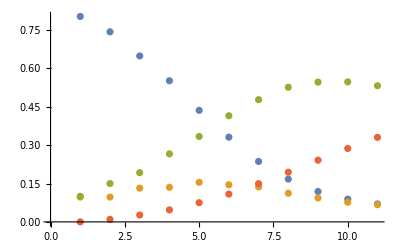

1

aa[1]

```mathematica
ListPlot[{
Table[s[t],{t,0,tmax,τ}],
Table[e[t],{t,0,tmax,τ}],
Table[infect[t],{t,0,tmax,τ}],
Table[r[t],{t,0,tmax,τ}]
}]
```

## Model SEIRS

```mathematica
SEIRS={
s'[t]==-β k s[t]i[t]+γ r[t],
e'[t]==β k i[t]s[t]-β k i[t-τ1]s[t-τ1],
i'[t]==β k i[t-τ1]s[t-τ1]- μ i[t]-d i[t],
r'[t]==μ i[t]-γ r[t],
r[t/;t<=0]==0,
i[t/;t<=0]==0.1,
e[t/;t<=0]==k i[t/;t<=0],
s[t/;t<=0]==1-e[t/;t<=0]-i[t/;t<=0]
};
tmax=100;
```

```mathematica
solution=ParametricNDSolveValue[SEIRS,{s,e,i,r},{t,-1,tmax},{β,μ,k,γ,d,τ1}];
Manipulate[Plot[Evaluate[#[t]&/@solution[β,μ,k,γ,d,τ1]],{t,-1,tmax},PlotLegends->{s,e,i,r},PlotRange->{-0.2,1}],{{β,0.77},0,1},{{μ,0.1},0,1},{{k,0.97},0,1},{{γ,0.037},0,1},{{d,0},0,1},{{τ1,1},1,15,1}]
```